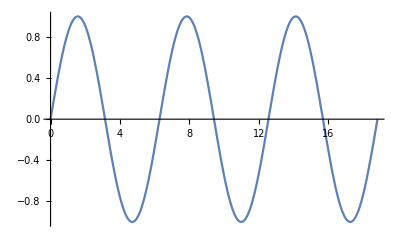

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

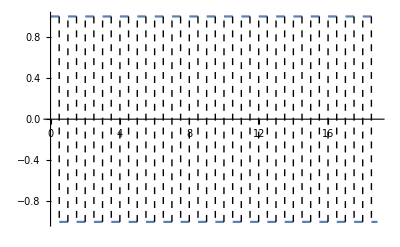

```mathematica
Plot[SquareWave[{-1,1},x],{x,0,6Pi},ExclusionsStyle->Dashed]
```

```mathematica
squareWave[t_,period_,duty_]:=UnitBox[Mod[t/period,1.]/(2. duty)]
```

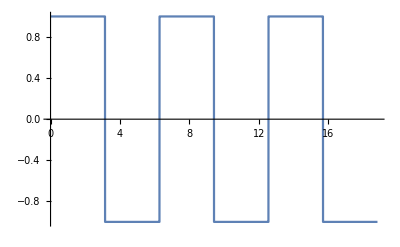

```mathematica
Plot[2*(squareWave[t,2*Pi,0.5]-0.5),{t,0,6*Pi}]
```

```mathematica
square = 2*(squareWave[x,2*Pi,0.5]-0.5)
```

2 (-0.5+UnitBox[1. Mod[x/(2 π),1.]])

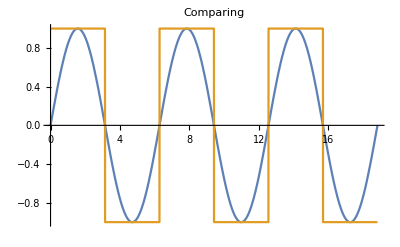

```mathematica
Plot[{Sin[x],square},{x,0,6 Pi},PlotLabel->"Comparing"]
```

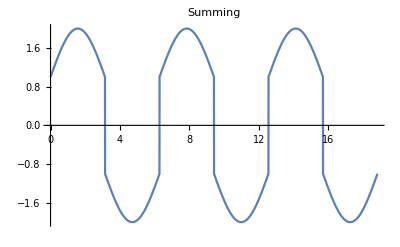

```mathematica
Plot[{Sin[x]+square},{x,0,6 Pi},PlotLabel->"Summing"]
```

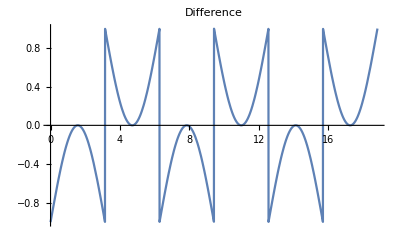

```mathematica
Plot[{Sin[x]-square},{x,0,6 Pi},PlotLabel->"Difference"]
```

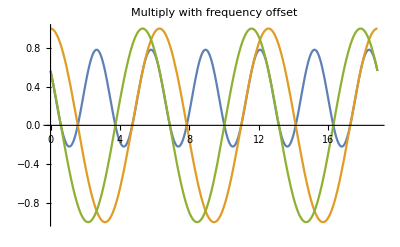

```mathematica
Plot[{Cos[x]*Cos[x+1000],Cos[x],Cos[x+1000]},{x,0,6 Pi},PlotLabel->"Multiply with frequency offset"]
```

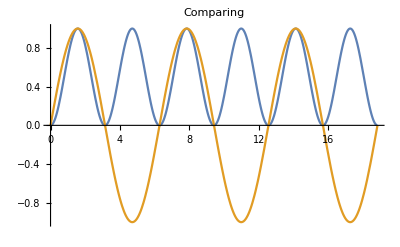

```mathematica
Plot[{Sin[x]*Sin[x],Sin[x]},{x,0,6 Pi},PlotLabel->"Comparing"]
```

```mathematica
Plot[{SquareWave[x]*SquareWave[x],SquareWave[x]},{x,0.6*Pi}]
```

Plot::pllim: Range specification {x, 0.6\ π} is not of the form {x, xmin, xmax}.

```mathematica
Plot[{SquareWave[x] SquareWave[x],SquareWave[x]},{x,,0,0.6* π}]
```

Plot::plln: Limiting value Null in {x, Null, 0, 0.6\ π} is not a machine-sized real number.

```mathematica
Plot[{SquareWave[x] SquareWave[x],SquareWave[x]}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

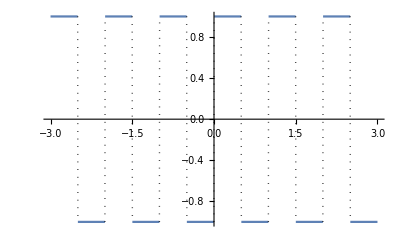

```mathematica
Plot[{SquareWave[x]},{x,-3,3},ExclusionsStyle->Dotted]
```

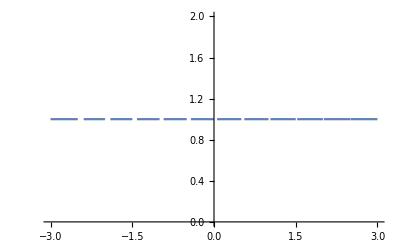

```mathematica
Plot[{SquareWave[x]*SquareWave[x]},{x,-3,3},ExclusionsStyle->Red]
```

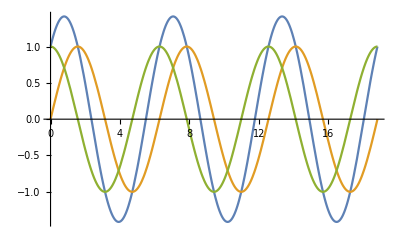

```mathematica
Plot[{Sin[x]+Cos[x],Sin[x],Cos[x]},{x,0,6*Pi}]
```